```mathematica
EvaluateToStart = "EvaluateToStart"
```

EvaluateToStart

```mathematica
ClearAll["Global`*"]
```

# Master Peoject Notebook

## Dirac Basis

## Preparation to calculate Bogoliubov coefficients

## Matrices Definition

```mathematica
σ= {{{1,0},{0,1}},{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
σto={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}},{{0, 0, -I, 0}, {0, 0, 0, -I}, {I, 0, 0, 0}, {0, I, 0, 0}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}};

otτ={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}},{{0, -I, 0, 0}, {I, 0, 0, 0}, {0, 0, 0, -I}, {0, 0, I, 0}},{{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}};
τ = {ArrayFlatten[{{otτ[[1]],0},{0,otτ[[1]]}}],ArrayFlatten[{{otτ[[2]],0},{0,otτ[[2]]}}],ArrayFlatten[{{otτ[[3]],0},{0,otτ[[3]]}}],ArrayFlatten[{{otτ[[4]],0},{0,otτ[[4]]}}]};
{τ[[1]]//MatrixForm,τ[[2]]//MatrixForm,τ[[3]]//MatrixForm,τ[[4]]//MatrixForm};
γD = {ArrayFlatten[{{σto[[1]],0},{0,-σto[[1]]}}],ArrayFlatten[{{0,σto[[2]]},{-σto[[2]],0}}],ArrayFlatten[{{0,σto[[3]]},{-σto[[3]],0}}],ArrayFlatten[{{0,σto[[4]]},{-σto[[4]],0}}]};
{γD[[1]]//MatrixForm,γD[[2]]//MatrixForm,γD[[3]]//MatrixForm,γD[[4]]//MatrixForm};
```

## Finding EigenValues[] and EigenVectors[]

```mathematica
DiracHamiltonianD=-M[η]*γD[[1]]-γD[[1]].γD[[4]]*k+f[η]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}]);
AnsD=FullSimplify[Eigensystem[-M[η]*γD[[1]]-γD[[1]].γD[[4]]*k+f[η]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}])]];
ωD = Table[AnsD[[1]][[i]],{i,1,8}];
uD = Table[AnsD[[2]][[i]],{i,1,8}];
fωD[η_,k_]:={-1/2 √((-2 k+f[η])^2+4 M[η]^2),1/2 √((-2 k+f[η])^2+4 M[η]^2),-1/2 √((2 k+f[η])^2+4 M[η]^2),1/2 √((2 k+f[η])^2+4 M[η]^2),-1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),-1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))}
```

### Simplifying EigenVectors

```mathematica
suD=Table[0,{i,1,8}];
```

```mathematica
suD[[1]]=uD[[1]];
suD[[1]]=Simplify[uD[[1]]/.√((-2 k+f[η])^2+4 M[η]^2)->2ω1 ];
suD[[1]]=√(ω1-M[η])suD[[1]]/. (2 k-f[η])->2*Sign[2 k-f[η]]*√(ω1^2-M[η]^2);
suD[[1]]=suD[[1]]/.(√(ω1-M[η])(ω1+M[η]))/(√(ω1^2-M[η]^2))->√(ω1+M[η]);
```

```mathematica
suD[[2]]=Simplify[uD[[2]]/.√((-2 k+f[η])^2+4 M[η]^2)->2ω1 ];
suD[[2]]=√(ω1+M[η])suD[[2]]/. (2 k-f[η])->2*Sign[2 k-f[η]]*√(ω1^2-M[η]^2);
suD[[2]]=suD[[2]]/.((ω1-M[η])√(ω1+M[η]))/(√(ω1^2-M[η]^2))->√(ω1-M[η]);
```

```mathematica
suD[[3]]=Simplify[uD[[3]]/.√((2 k+f[η])^2+4 M[η]^2)->2ω2 ];
suD[[3]]=√(ω2-M[η])suD[[3]]/. (2 k+f[η])->2*Sign[2 k+f[η]]*√(ω2^2-M[η]^2);
suD[[3]]=suD[[3]]/.(√(ω2-M[η])(ω2+M[η]))/(√(ω2^2-M[η]^2))->√(ω2+M[η]);
```

```mathematica
suD[[4]]=Simplify[uD[[4]]/.√((2 k+f[η])^2+4 M[η]^2)->2ω2 ];
suD[[4]]=√(ω2+M[η])suD[[4]]/. (2 k+f[η])->2*Sign[2 k+f[η]]*√(ω2^2-M[η]^2);
suD[[4]]=suD[[4]]/.((ω2-M[η])√(ω2+M[η]))/(√(ω2^2-M[η]^2))->√(ω2-M[η]);
```

```mathematica
suD[[5]]=Simplify[uD[[5]]/.√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω3 ];
suD[[5]]=√(ω3-M[η])suD[[5]]/.√(ω3-M[η]) (ω3+M[η])->√(ω3^2-M[η]^2)√(ω3+M[η]);
suD[[5]]=suD[[5]]/.√(ω3^2-M[η]^2)->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=Simplify[suD[[5]]/.k^2+(5 f[η]^2)/4-√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)-(√(f[η]^2))/2)^2];
suD[[5]]=√(1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[5]]/.√(1/2 √(f[η]^2)+√(k^2+f[η]^2))√((-1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(-1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[5]]=√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[5]]/.√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2)));

suD[[5]]=suD[[5]]/.(2 f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2 f[η])/(f[η]^2-2  √(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=suD[[5]]/.(2 f[η])/(f[η]2-2  √(f[η]^2 (k^2+f[η]^2)))->(-2 f[η])/(-f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=1/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[5]]/.2/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->-2/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[5]] = suD[[5]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4);
```

```mathematica
suD[[6]]=Simplify[uD[[6]]/.√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω3 ];
suD[[6]]=√(ω3+M[η])suD[[6]]/.√(ω3+M[η]) (ω3-M[η])->√(ω3^2-M[η]^2)√(ω3-M[η]);
suD[[6]]=suD[[6]]/.√(ω3^2-M[η]^2)->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=Simplify[suD[[6]]/.k^2+(5 f[η]^2)/4-√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)-(√(f[η]^2))/2)^2];
suD[[6]]=√(1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[6]]/.√((-1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) √(1/2 √(f[η]^2)+√(k^2+f[η]^2))->√(k^2+3/4 f[η]^2)√(-1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[6]]=suD[[6]]/.(2(k f[η]-√(f[η]^2 (k^2+f[η]^2)))) ->-2(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) ;
suD[[6]]=√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[6]]/.√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=suD[[6]]/.(-2*f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(-2* f[η])/(f[η]^2-2  √(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=suD[[6]]/.(-2*f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2* f[η])/(-f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=1/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[6]]/.-2/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->2/(2 √(f[η]^2 k^2+3/4 f[η]^4)√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[6]] = suD[[6]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4);
```

```mathematica
suD[[7]]=Simplify[uD[[7]]/. √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω4 ];
suD[[7]]=√(ω4-M[η])suD[[7]]/.√(ω4-M[η]) (ω4+M[η])->√(ω4^2-M[η]^2)√(ω4+M[η]);
suD[[7]]=suD[[7]]/.√(ω4^2-M[η]^2)->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=Simplify[suD[[7]]/.k^2+(5 f[η]^2)/4+√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)+(√(f[η]^2))/2)^2];
suD[[7]]=√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[7]]/.√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))√((1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[7]]=√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[7]]/.√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=suD[[7]]/.(-2 f[η]^2)/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(-2 f[η])/(f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[7]]/.1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->1/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[7]] = suD[[7]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4);
```

```mathematica
suD[[8]]=Simplify[uD[[8]]/. √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω4 ];
suD[[8]]=√(ω4+M[η])suD[[8]]/.√(ω4+M[η]) (ω4-M[η])->√(ω4^2-M[η]^2)√(ω4-M[η]);
suD[[8]]=suD[[8]]/.√(ω4^2-M[η]^2)->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=Simplify[suD[[8]]/.k^2+(5 f[η]^2)/4+√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)+(√(f[η]^2))/2)^2];
suD[[8]]=√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[8]]/.√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))√((1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[8]]=√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[8]]/.√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=suD[[8]]/.(2 f[η]^2)/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2 f[η])/(f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[8]]/.1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->1/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[8]] = suD[[8]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4);
```

```mathematica
nsuD = suD;
nsuD[[1]] = 1/(√(2*ω1))*nsuD[[1]];
nsuD[[2]]= 1/(√(2*ω1))*nsuD[[2]];
nsuD[[3]] = 1/(√(2*ω2))*nsuD[[3]];
nsuD[[4]] = 1/(√(2*ω2))*nsuD[[4]];
nsuD[[5]]=1/(√(2*ω3*√(k^2+f[η]^2)))*nsuD[[5]];
nsuD[[6]]=1/(√(2*ω3*√(k^2+f[η]^2)))*nsuD[[6]];
nsuD[[7]]=1/(√(2*ω4*√(k^2+f[η]^2)))*nsuD[[7]];
nsuD[[8]]=1/(√(2*ω4*√(k^2+f[η]^2)))*nsuD[[8]];
```

### Check that simplifying went correct

```mathematica
(* check scalar product *)
errors =0;
For[i=1,i<=8,i++,
 For[j=1,j<=i,j++,
  product = Assuming[k>0&&f[η]>0,FullSimplify[Dot[nsuD[[i]],nsuD[[j]]]]];
  product=product/.Sign[2 k-f[η]]^2->1;
  product=product/.Sign[2 k+f[η]]^2->1;
  product=product/.√(ω3-M[η]) √(ω3+M[η])->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
  product=product/.√(f[η]^2) (k^2+f[η]^2)-√(k^2+f[η]^2) √(f[η]^2 (k^2+f[η]^2))->0;
  product=product/.√(ω4-M[η]) √(ω4+M[η])->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
  product=product/.-f[η]^2 √(k^2+f[η]^2)+√(f[η]^2) √(f[η]^2 (k^2+f[η]^2))->0;
  product=product/.ω3->1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2));
  product=product/.ω4->1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2));
  product=product/.√(-2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))->√2(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)));
         product=Simplify[product/.√(2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))->√2(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))];       
  product=product/.k f[η]-√(f[η]^2 (k^2+f[η]^2))+√(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->0;
         
If[i==j && (product===0) , errors++; Print[i,j, product]];  
  If[i!=j && !(product===0) , errors++;Print[i,j,product]];
]
]
If[errors==0,Print[True];];
If[errors!=0,Print[False];];
```

True

```mathematica
Table[ Assuming[k>0&&f[η]>0,FullSimplify[Dot[nsuD[[i]],nsuD[[j]]]]],{i,1,8},{j,1,8}];
```

```mathematica
(* check that suD are proportional to uD*)
errors = 0;
For[i=1, i<=8, i++,
	multiplier=0;
	For[j=1,j<=8,j++,
		If[uD[[i]][[j]]===1,
			multiplier = suD[[i]][[j]];
		];
	];
	muD = multiplier* uD[[i]];
	For[j=1,j<=8,j++,
		If[suD[[i]][[j]]===0 && muD[[j]] != 0,
			Print["Error for: ",i,j];
			errors += 1;
		];
		If[!suD[[i]][[j]]===0,
			If[! Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]==1]],
				Print["Error for: ",i,j, "got:",Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]]], muD[[j]], uD[[i]][[j]]];
				errors+=1;
			];
		];
	]
]
If[errors == 0, Print[True],Print[False]]
```

True

## derivatives of eigenvectors, products of eigenvectors derivatives and eigenvectors

```mathematica
dnsuD= Table[D[nsuD[[i]],η],{i,1,8}];
```

### scalar product of eigenvectors and its derivatives

```mathematica
productsD=Table[Dot[nsuD[[i]],dnsuD[[j]]],{i,1,8},{j,1,8}];
productsD//MatrixForm;
productsD==Assuming[f[η]>0 && k >0&&M[η]>0, FullSimplify[productsD]];
```

### check that up and down do not mix

```mathematica
errors =0;
For[i=3,i<=4,i++,
  For[j=1,j<=2,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=1,i<=2,i++,
  For[j=3,j<=4,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=5,i<=8,i++,
  For[j=1,j<=4,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=1,i<=4,i++,
  For[j=5,j<=8,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
If[errors ==0, Print[True]]
```

True

```mathematica
productsD1 = Table[FullSimplify[productsD[[i]][[j]]],{i,1,2},{j,1,2}];
```

```mathematica
productsD2 = Table[FullSimplify[productsD[[i]][[j]]],{i,3,4},{j,3,4}];
```

```mathematica
productsD3 = Table[FullSimplify[productsD[[i]][[j]]],{i,5,8},{j,5,8}];
```

#### Mixing of aup-up (assumption: Sign'[2 k-f[η]]->0)

```mathematica
sproductsD1 =Assuming[k>0&& M[η]>0&&ω1 > M[η]&&f[η]>0 && 2k!=f[η],FullSimplify[productsD1/.1/Sign[2 k-f[η]]^2->1/.Sign[2 k-f[η]]^2->1/.Sign'[2 k-f[η]]->0]]
```

{{0,M'[η]/(2 √(ω1^2-M[η]^2))},{-M'[η]/(2 √(ω1^2-M[η]^2)),0}}

#### Mixing of adown-down(assumption: Sign'[2 k-f[η]]->0)

```mathematica
sproductsD2 =FullSimplify[Assuming[k>0&& M[η]>0&&ω2 > M[η]&&f[η]>0,FullSimplify[productsD2/.1/Sign[2 k-f[η]]^2->1/.Sign[2 k-f[η]]^2->1/.Sign'[2 k-f[η]]->0]]/.Sign'[2 k+f[η]]->0]
```

{{0,M'[η]/(2 √(ω2^2-M[η]^2))},{-M'[η]/(2 √(ω2^2-M[η]^2)),0}}

### Mixed part

```mathematica
sproductsD3=Assuming[k>0&& M[η]>0&&ω1 > M[η]&&f[η]>0,FullSimplify[productsD3]]
```

{{0,M'[η]/(2 √(ω3-M[η]) √(ω3+M[η])),(k (√(ω3-M[η]) √(ω4-M[η])-√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2))},{-M'[η]/(2 √(ω3-M[η]) √(ω3+M[η])),0,(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (-√(ω3-M[η]) √(ω4-M[η])+√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2))},{(k (-√(ω3-M[η]) √(ω4-M[η])+√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),-(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),0,M'[η]/(2 √(ω4-M[η]) √(ω4+M[η]))},{-(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (√(ω3-M[η]) √(ω4-M[η])-√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),-M'[η]/(2 √(ω4-M[η]) √(ω4+M[η])),0}}

### Combine into one 8x8 matrix and then split into four 4x4 matrices

```mathematica
Combined=DiagonalMatrix[Hold/@{sproductsD1,sproductsD2,sproductsD3}]//ReleaseHold//ArrayFlatten;
Combined;
Combined = Combined /.ω1-> ωD[[2]]/.ω2-> ωD[[4]]/.ω3-> ωD[[6]]/.ω4-> ωD[[8]];fCombined[a_,b_]:=Combined/.η->a/.k->b
```

### Dump to memory before defining f[t] and M[t]

```mathematica
DumpSave["ωD.mx",ωD];
DumpSave["uD.mx",uD];
DumpSave["nsuD.mx",nsuD];
DumpSave["dnsuD.mx",dnsuD];
DumpSave["sproductsD1.mx",sproductsD1];
DumpSave["sproductsD2.mx",sproductsD2];
DumpSave["sproductsD3.mx",sproductsD3];
DumpSave["Combined.mx",Combined];
DumpSave["fCombined.mx",fCombined];
DumpSave["fωD.mx",fωD];
```

## Bogoliubov coefficients calculation

### Get from memory

```mathematica
ClearAll["Global`*"]
```

```mathematica
Get["ωD.mx",ωD];
Get["uD.mx",uD];
Get["nsuD.mx",nsuD];
Get["dnsuD.mx",dnsuD];
Get["sproductsD1.mx",sproductsD1];
Get["sproductsD2.mx",sproductsD2];
Get["sproductsD3.mx",sproductsD3];
Get["Combined.mx",Combined];
Get["fCombined.mx",fCombined];
Get["fωD.mx",fωD];
```

### Define Matrices

```mathematica
a[η_]={{a11[η],a12[η],a13[η],a14[η]},{a21[η],a22[η],a23[η],a24[η]},{a31[η],a32[η],a33[η],a34[η]},{a41[η],a42[η],a43[η],a44[η]}};
b[η_]={{b11[η],b12[η],b13[η],b14[η]},{b21[η],b22[η],b23[η],b24[η]},{b31[η],b32[η],b33[η],b34[η]},{b41[η],b42[η],b43[η],b44[η]}};
(*phasesPlus[η1_]:=Table[Exp[2*I*NIntegrate[fωD[t][[2*i]],{t,start,η1}]],{i,1,4}]
phasesMinus[η1_]:=Table[Exp[-2*I*NIntegrate[fωD[t][[2*i]],{t,start,η1}]],{i,1,4}]*)
```

```mathematica
Table[Combined[[2i-1]][[2j-1]],{i,1,4},{j,1,4}];
```

```mathematica
A1[η_,k_]:=Table[fCombined[η,k]⟦2 i⟧⟦2 j⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
A2[η_,k_]:=Table[fCombined[η,k]⟦2 i⟧⟦2 j-1⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
B1[η_,k_]:=Table[fCombined[η,k]⟦2 i-1⟧⟦2 j⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
B2[η_,k_]:=Table[fCombined[η,k]⟦2 i-1⟧⟦2 j-1⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
```

```mathematica
AA2[a_,b_]=Table[Evaluate[If[i==1 && j ==1,0,A2[η,k][[i]][[j]]]]/.η->a/.k->b,{i,1,4},{j,1,4}];
BB1[a_,b_]=Table[Evaluate[If[i==1 && j ==1,0,B1[η,k][[i]][[j]]]]/.η->a/.k->b,{i,1,4},{j,1,4}];
mA2[η_,k_]:=Piecewise[{{A2[η,k], -2*η*k !=f1}, {AA2[η,k], True}}]
mB1[η_,k_]:=Piecewise[{{B1[η,k], -2*η*k !=f1}, {BB1[η,k], True}}]
```

```mathematica
Ph[η_] = {Ph1[η],Ph2[η],Ph3[η],Ph4[η]};
ExpPhPlus[η_]={Exp[2*I*Ph1[η]],Exp[2*I*Ph2[η]],Exp[2*I*Ph3[η]],Exp[2*I*Ph4[η]]};
ExpPhMinus[η_]={Exp[-2*I*Ph1[η]],Exp[-2*I*Ph2[η]],Exp[-2*I*Ph3[η]],Exp[-2*I*Ph4[η]]};
```

### No-mass check

```mathematica
M1=0;
f1=5;
M[η_]:=-M1/η;
f[η_]:=-f1/η;
df[η_]:=f'[η];
start = -2;
stop = -0.02;
fnoMsol[k_] := NDSolve[{
a'[η]==a[η].A1[η,k] + Transpose[ExpPhPlus[η]*Transpose[b[η].B1[η,k]]],
b'[η]== Transpose[ExpPhMinus[η]*Transpose[a[η].A2[η,k]]]+ b[η].B2[η,k],
Ph1'[η]==fωD[η,k][[2]],Ph2'[η]==fωD[η,k][[4]],Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
a[start]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},
b[start]=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},
Ph1[start]==0,Ph2[start]==0,Ph3[start]==0,Ph4[start]==0},
{a11[η],a12[η],a13[η],a14[η],a21[η],a22[η],a23[η],a24[η],a31[η],a32[η],a33[η],a34[η],a41[η],a42[η],a43[η],a44[η],b11[η],b12[η],b13[η],b14[η],b21[η],b22[η],b23[η],b24[η],b31[η],b32[η],b33[η],b34[η],b41[η],b42[η],b43[η],b44[η],Ph1[η],Ph2[η],Ph3[η],Ph4[η]},
{η,start,stop}];
```

```mathematica
Table[Plot[Evaluate[Abs[(a[η][[i]][[j]])^2]/.fnoMsol[0.1]],{η,start,stop}, PlotRange->All],{i,1,4},{j,1,4}];
```

```mathematica
Table[Plot[Evaluate[Abs[(b[η][[i]][[j]])^2]/.fnoMsol[0.1]],{η,start,stop}, PlotRange->All],{i,1,4},{j,1,4}];
```

```mathematica
NN[n_]:= 10.4^(1+3*(n/200)^3) 
noMkdependence34 = Table[{NN[n]/f1,Evaluate[Abs[b34[η]]/.fnoMsol[NN[n]]/.η->stop][[1]]},{n,-200,200}];
```

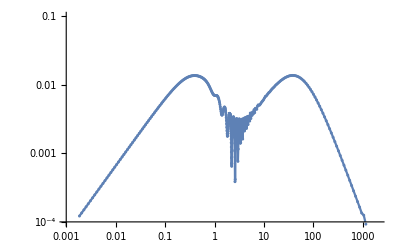

```mathematica
noMb34Plot = ListLogLogPlot[noMkdependence34,PlotRange->{{10^-3,2*10^3},{10^-4, 10^-1}},PlotMarkers->{Automatic,3}, Joined->True]
```

```mathematica
noMkdependence43= Table[{NN[n]/f1,Evaluate[Abs[b43[η]]/.fnoMsol[NN[n]]/.η->stop][[1]]},{n,-200,200}];
```

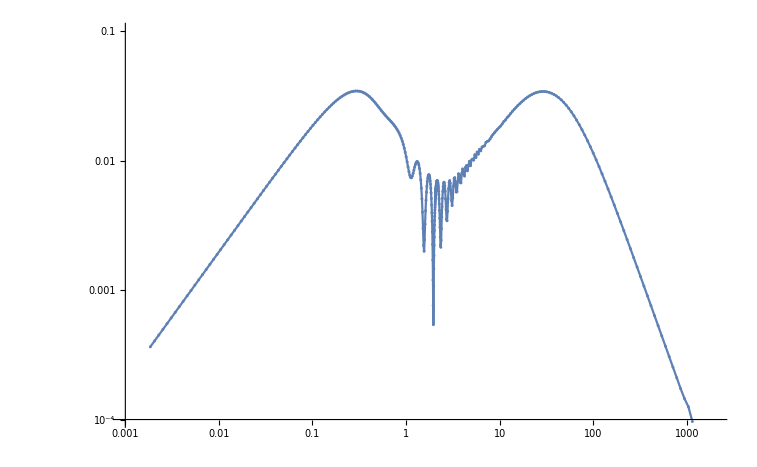

```mathematica
ListLogLogPlot[noMkdependence43,PlotRange->{{10^-3,2*10^3},{10^-4, 10^-1}},PlotMarkers->{Automatic,3}, Joined->True]
```

### Define functions

```mathematica
start = -2;
stop = -0.02;
ϵ1=0.1;
ϵ2 = 0.001;
f1=5;
f2=0;
M1=1;
f[η_]:=Piecewise[{{f1/2, η<=-2}, {-f1/η, -2<η<=-0.02}, {f1/0.02, True}}]
```

```mathematica
df[η_]:=Piecewise[{{0, η<=-2}, {f1/η^2, -2<η<-0.02}, {0, True}}]
```

```mathematica
M[η_]:=-M1/η;
```

### Solve for Bogoliubov coefficients

```mathematica
sol = NDSolve[{
a'[η]==a[η].A1[η,5] + Transpose[ExpPhPlus[η]*Transpose[b[η].Evaluate[BB1[η,5]]]]/.f'[η]->df[η],
b'[η]== Transpose[ExpPhMinus[η]*Transpose[a[η].Evaluate[AA2[η,5]]]]+ b[η].B2[η,5]/.f'[η]->df[η],
Ph1'[η]==fωD[η,5][[2]],Ph2'[η]==fωD[η,5][[4]],Ph3'[η]==fωD[η,5][[6]],Ph4'[η]==fωD[η,5][[8]]/.f'[η]->df[η],
a[start]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},
b[start]=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}, 
Ph1[start]==0,Ph2[start]==0,Ph3[start]==0,Ph4[start]==0
},{a11[η],a12[η],a13[η],a14[η],a21[η],a22[η],a23[η],a24[η],a31[η],a32[η],a33[η],a34[η],a41[η],a42[η],a43[η],a44[η],b11[η],b12[η],b13[η],b14[η],b21[η],b22[η],b23[η],b24[η],b31[η],b32[η],b33[η],b34[η],b41[η],b42[η],b43[η],b44[η],Ph1[η],Ph2[η],Ph3[η],Ph4[η]},{η,start,stop},Method -> "StiffnessSwitching"];
```

```mathematica
fsol[k_] := NDSolve[{
a'[η]==a[η].A1[η,k] + Transpose[ExpPhPlus[η]*Transpose[b[η].mB1[η,k]]]/.f'[η]->df[η],
b'[η]== Transpose[ExpPhMinus[η]*Transpose[a[η].mA2[η,k]]]+ b[η].B2[η,k]/.f'[η]->df[η],
Ph1'[η]==fωD[η,k][[2]],Ph2'[η]==fωD[η,k][[4]],Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
a[start]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},
b[start]=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},
Ph1[start]==0,Ph2[start]==0,Ph3[start]==0,Ph4[start]==0},{a11[η],a12[η],a13[η],a14[η],a21[η],a22[η],a23[η],a24[η],a31[η],a32[η],a33[η],a34[η],a41[η],a42[η],a43[η],a44[η],b11[η],b12[η],b13[η],b14[η],b21[η],b22[η],b23[η],b24[η],b31[η],b32[η],b33[η],b34[η],b41[η],b42[η],b43[η],b44[η],Ph1[η],Ph2[η],Ph3[η],Ph4[η]},
{η,start,stop},Method -> "StiffnessSwitching"];
```

```mathematica
NN[n_]:= 10.4^(1+3*(n/200)^3) 
kdependence34 = Table[{NN[n]/f1,Evaluate[Abs[b34[η]]/.fsol[NN[n]]/.η->stop][[1]]},{n,-200,200}];
```

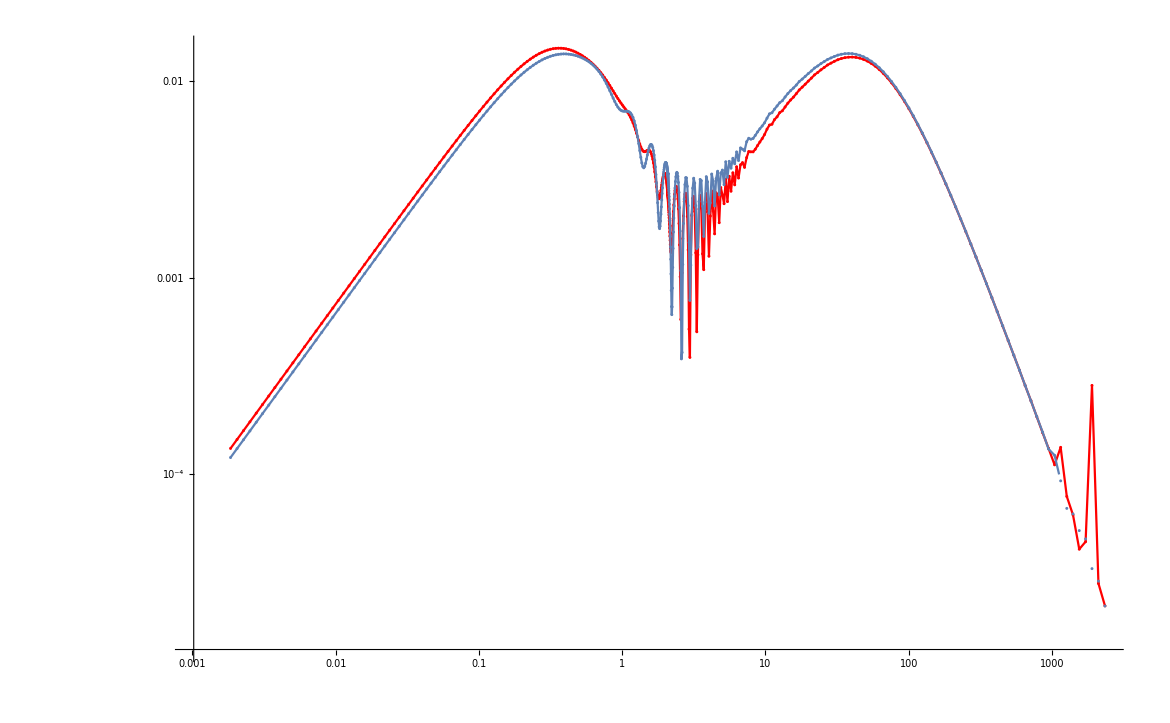

```mathematica
b34Plot=ListLogLogPlot[kdependence34, PlotRange->All, PlotStyle->Red,PlotMarkers->{Automatic,3}, Joined->True];
Show[b34Plot,noMb34Plot]
```

```mathematica
kdependence22 = Table[{NN[n]/f1,Evaluate[Abs[b22[η]]/.fsol[NN[n]]/.η->stop][[1]]},{n,-200,200}];
```

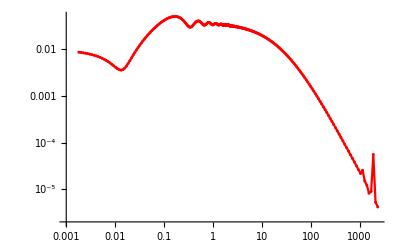

```mathematica
b22Plot=ListLogLogPlot[kdependence22, PlotRange->All, PlotStyle->Red,PlotMarkers->{Automatic,3}, Joined->True]
```

# Artifacts

```mathematica
fconnect2[x_,a_,b_]:=1/(2 a^2(a-b))(x-b)^2;
a1 = - 2-ϵ1;
b1   = -2+ϵ1;
a2 = - 0.02-ϵ2;
b2   = -0.02+ϵ2;
ff[η_]:=Piecewise[{
{f1*(-fconnect2[b1,b1,a1])+-f1/b1-f2, η< a1},
 {f1*(fconnect2[η,b1,a1]-fconnect2[b1,b1,a1])+-f1/b1-f2,a1<=η< b1},
{-f1/η -f2, b1<= η<a2},
{f1*(fconnect2[η,a2,b2]-fconnect2[a2,a2,b2]) + -f1/a2 -f2 ,a2<=η<b2},
{-f1/a2 -f2 - f1*fconnect2[a2,a2,b2], η>=b2}
},{η,start*2,0} ]; (*Make it picewise*)
```